```mathematica
ClearAll["Global`*"];

u=Simplify[(z zb )/.{z->(a+Sqrt[b])/2,zb-> (a-Sqrt[b])/2}]
v=Simplify[((1-z)(1-zb))/.{z->(a+Sqrt[b])/2,zb-> (a-Sqrt[b])/2}]
```

1/4 (a^2-b)

1/4 (4-4 a+a^2-b)

```mathematica
k[β_,x_]:=x^(β/N[2,20])*Hypergeometric2F1[β/N[2,20],β/N[2,20],β,x];

G[Δ_,l_,z_,zb_]:=N[0.5,20](k[Δ+l,z]k[Δ-l,zb]+k[Δ+l,zb]k[Δ-l,z]);
```

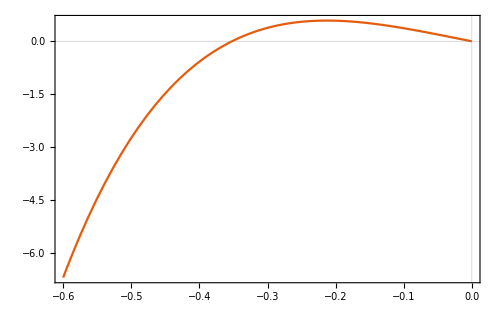

```mathematica
Plot[27.2528*(D[G[Δ,0,z,zb]/.{z->(a+Sqrt[b])/2,zb-> (a-Sqrt[b])/2},{a,2}]/.{a->1,b->0} )
-
 3.27106  (D[G[Δ,0,z,zb]/.{z->(a+Sqrt[b])/2,zb-> (a-Sqrt[b])/2},{a,4}]/.{a->1,b->0}),{Δ,-0.6,0},PlotTheme->"Scientific",ImageSize->500]
```

```mathematica
g[αΔ_,αl_,βΔ_,βl_]:= ((v^α *G[βΔ,βl,z,zb])-(u^α *G[βΔ,βl,1-z,1-zb]))/(u^α -v^α);

(*D[g[Δα,lα,Δβ,lβ]/.{z->(a+Sqrt[b])/2,zb->(a-Sqrt[b])/2},{b,3}]/.{a->1+10^-10,b->10^-10}*)
```

```mathematica
(*WriteMatrix[UnknownOperatorsList_,M_,N_]:=Module[
{mat},
derivlist={{0,1},{1,0},{1,1},{2,0},{0,2}};
mat=Table[D[D[,{a,2i}],{b,j}],{i,1,N},{j,1,N}];
Return[mat]
]*)
```

```mathematica
(*Plot[{G[ Δ,1,N[1/2,20],N[1/2,20]],2^Δ (1+1/(√2))^(-2 Δ) (1.03063798650705733902335856061`19.521390395643703-(0.01507188445002202955923146501334713246`19.144380726017946)/(-0.01`20.+Δ)+(1.17144629344727857235774302039`19.208322590815246*^-9)/(0.99`21.99563519459755+Δ)+(0.00073148689545185610892429186002227115`19.20833653580393)/(1.99`22.298853076409706+Δ)-(0.0166825446879360666983250051143683859`19.081545000250358)/(2+Δ)+(1.45586266322610214744356048774061573`19.208127545352344*^-12)/(2.99`22.475671188324434+Δ)-(0.00052991344307041722765795711871072777`18.370285104467747)/(4+Δ)-(0.00001626401694977143151264136141118267`17.615664176467888)/(6+Δ)-(4.8979241967524508859499612246149`16.85285577757625*^-7)/(8+Δ))},{ Δ,0,8}]*)
```

```mathematica
g4[Δ_,l_,z_,zb_]:=(z zb/(z-zb))*(k[Δ+l,z]*k[Δ-l-2,zb] - k[Δ+l,zb]*k[Δ-l-2,z] )
```

```mathematica
N20=N[#,20]&;
```

```mathematica
G[ Δ,N[3,20],z,zb]/.{z->(a+Sqrt[b])/2,zb->(a-Sqrt[b])/2}
```

0.5 (2^(-0.5 (-3.+Δ)-0.5 (3.+Δ)) (a-√b)^(0.5 (3.+Δ)) (a+√b)^(0.5 (-3.+Δ)) Hypergeometric2F1[0.5 (-3.+Δ),0.5 (-3.+Δ),-3.+Δ,1/2 (a+√b)] Hypergeometric2F1[0.5 (3.+Δ),0.5 (3.+Δ),3.+Δ,1/2 (a-√b)]+2^(-0.5 (-3.+Δ)-0.5 (3.+Δ)) (a-√b)^(0.5 (-3.+Δ)) (a+√b)^(0.5 (3.+Δ)) Hypergeometric2F1[0.5 (-3.+Δ),0.5 (-3.+Δ),-3.+Δ,1/2 (a-√b)] Hypergeometric2F1[0.5 (3.+Δ),0.5 (3.+Δ),3.+Δ,1/2 (a+√b)])

```mathematica
D[G[ Δ,N[0,20],z,zb]/.{z->(a+Sqrt[b])/2,zb->(a-Sqrt[b])/2}]
```

1. 2^(-1. Δ) (a-√b)^(0.5 Δ) (a+√b)^(0.5 Δ) Hypergeometric2F1[0.5 Δ,0.5 Δ,Δ,1/2 (a-√b)] Hypergeometric2F1[0.5 Δ,0.5 Δ,Δ,1/2 (a+√b)]

```mathematica
ΔLlist={{Δ,N20@0},{N20@2,N20@2}};
mnlist={{1,0},{2,0}};
```

```mathematica
mat={};
```

```mathematica
{{1,2},{3,4}}//MatrixForm
```

(1 | 2
3 | 4)

```mathematica
Table[Join[ΔLlist[[i]],mnlist[[j]]],{i,1,2},{j,1,2}]//MatrixForm
```

((Δ
0
1
0) | (Δ
0
2
0)
(2.
2.
1
0) | (2.
2.
2
0))

```mathematica
(*h[α_,d_,l_,z_,zb_]:=G[d,l,z,zb];(* ((4-4 a+a^2-b)^(α)G[d,l,z,zb]  -(a^2-b)^α  G[d,l,z,zb]) /((a^2-b)^α-(4-4 a+a^2-b)^(α) );*)
```

Power::infy: Infinite expression 1/0.^2 encountered.

Infinity::indet: Indeterminate expression ComplexInfinity + ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression ComplexInfinity + ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ComplexInfinity + ComplexInfinity + ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

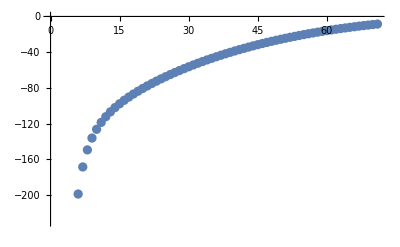

```mathematica
ListPlot[Det[


{

{D[h[ Δ,Δ,N[0,10],z,zb]/.{z->(a+Sqrt[b])/2,zb->(a-Sqrt[b])/2},{a,2}]/.{a->1,b-> 0},D[h[ Δ,Δ,N[0,10],z,zb]/.{z->(a+Sqrt[b])/2,zb->(a-Sqrt[b])/2},{a,4}]/.{a->1,b-> 0}
},


{

D[h[ Δ,2,N[2,10],z,zb]/.{z->(a+Sqrt[b])/2,zb->(a-Sqrt[b])/2},{a,2}]/.{a->1,b-> 0},

D[h[ Δ,2,N[2,10],z,zb]/.{z->(a+Sqrt[b])/2,zb->(a-Sqrt[b])/2},{a,2}]/.{a->1,b-> 0}

}

}]/.{Δ->#}&@Table[i,{i,-1,-0.3,0.01}]]*)
```

```mathematica
D[h[ Δ,Δ,N[0,20],z,zb]/.{z->(a+Sqrt[b])/2,zb->(a-Sqrt[b])/2},{a,2}]/.{a->N[1.0001,10],b-> N[0.0001,10]}
```

1.0101^(0.5 Δ) (0.+0.5 0.9901^(-2+0.5 Δ) 2^(-1. Δ) (-1+0.5 Δ) Δ) Hypergeometric2F1[0.5 Δ,0.5 Δ,Δ,0.49505] Hypergeometric2F1[0.5 Δ,0.5 Δ,Δ,0.50505]+1. 0.9901^(-1+0.5 Δ) 2^(-1. Δ) Δ (0.125 1.0101^(0.5 Δ) Δ Hypergeometric2F1[1+0.5 Δ,1+0.5 Δ,1+Δ,0.50505] Hypergeometric2F1[0.5 Δ,0.5 Δ,Δ,0.49505]+0.125 1.0101^(0.5 Δ) Δ Hypergeometric2F1[1+0.5 Δ,1+0.5 Δ,1+Δ,0.49505] Hypergeometric2F1[0.5 Δ,0.5 Δ,Δ,0.50505]+0.5 1.0101^(-1+0.5 Δ) Δ Hypergeometric2F1[0.5 Δ,0.5 Δ,Δ,0.49505] Hypergeometric2F1[0.5 Δ,0.5 Δ,Δ,0.50505])+1. 0.9901^(0.5 Δ) 2^(-1. Δ) (1/(1+Δ)0.0625 1.0101^(0.5 Δ) (1+0.5 Δ)^2 Δ Hypergeometric2F1[2+0.5 Δ,2+0.5 Δ,2+Δ,0.50505] Hypergeometric2F1[0.5 Δ,0.5 Δ,Δ,0.49505]+0.25 Δ Hypergeometric2F1[1+0.5 Δ,1+0.5 Δ,1+Δ,0.50505] (0.125 1.0101^(0.5 Δ) Δ Hypergeometric2F1[1+0.5 Δ,1+0.5 Δ,1+Δ,0.49505]+0.5 1.0101^(-1+0.5 Δ) Δ Hypergeometric2F1[0.5 Δ,0.5 Δ,Δ,0.49505])+(0.125 1.0101^(-1+0.5 Δ) Δ^2 Hypergeometric2F1[1+0.5 Δ,1+0.5 Δ,1+Δ,0.49505]+(0.0625 1.0101^(0.5 Δ) (1+0.5 Δ)^2 Δ Hypergeometric2F1[2+0.5 Δ,2+0.5 Δ,2+Δ,0.49505])/(1+Δ)+0.5 1.0101^(-2+0.5 Δ) (-1+0.5 Δ) Δ Hypergeometric2F1[0.5 Δ,0.5 Δ,Δ,0.49505]) Hypergeometric2F1[0.5 Δ,0.5 Δ,Δ,0.50505])

```mathematica
D[D[(u^α)/(u^α - v^α),{a,0}],{b,1}]/.{a->1,b->0}
```

Power::infy: Infinite expression 1/0 encountered.

Power::infy: Infinite expression 1/0^2 encountered.

Infinity::indet: Indeterminate expression 0\ 4^-α\ ComplexInfinity encountered.

Indeterminate